```mathematica
Limit[(Sqrt[Cos[2x]+1]-Sqrt[Cos[3x]+1])/Log[x^2+1],x->0]
```

5/(4 √2)

```mathematica
N[5/(4 √2)]
```

0.883883

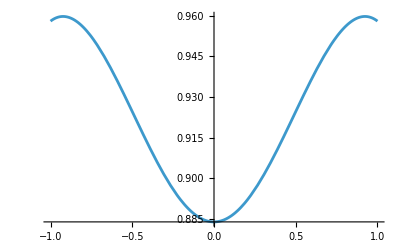

```mathematica
Plot[(Sqrt[Cos[2x]+1]-Sqrt[Cos[3x]+1])/Log[x^2+1], {x, -1, 1}]
```

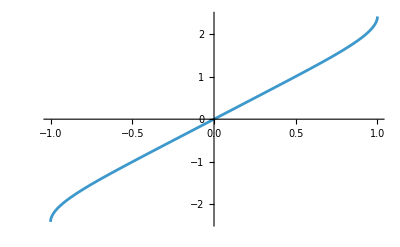

```mathematica
Plot[Sin[x]+ArcSin[x],{x,-1,1}]
```

```mathematica
Series[Sin[x],{x, 0, 5}]
Series[ArcSin[x],{x, 0,5}]
```

x-x^3/6+x^5/120+O[x]^6

x+x^3/6+(3 x^5)/40+O[x]^6

```mathematica
"Druhý člen rozvoje se vyruší"
```

```mathematica
Normal[Series[Cos[x],{x, 0,8}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

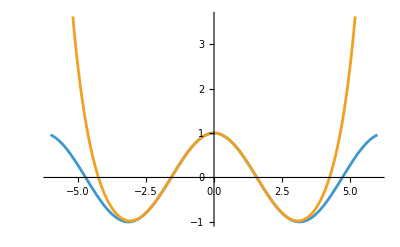

```mathematica
Plot[{Cos[x],1-x^2/2+x^4/24-x^6/720+x^8/40320},{x, -6, 6}]
```

```mathematica
f[x_]:=42x^6-126x^5+105x^4-21x^2+1
Solve[D[f[x],x]==0,x, Reals]
```

{{x→0},{x→1/2},{x→1},{x→1/6 (3-√21)},{x→1/6 (3+√21)}}

```mathematica
ddf[x_]=D[D[f[x],x],x]
ddf[0] < 0
ddf[1/2]> 0
ddf[1]< 0
ddf[1/6 (3-√21)]> 0
ddf[1/6 (3+√21)]> 0
```

-42+1260 x^2-2520 x^3+1260 x^4

True

True

True

«2 more identical outputs»

```mathematica
"Lokální extrémy na intervalu"
```

```mathematica
Maximize[{f[x],-1<=x<=2},x]
Minimize[{f[x],-1<=x<=2},x]
```

{253,{x→-1}}

{-31/32,{x→1/2}}

```mathematica
"Globální extrémy na intervalu"
```

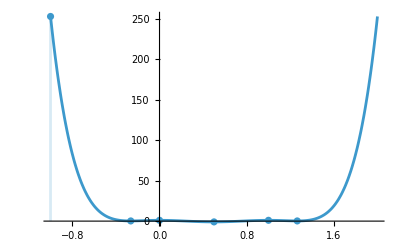

```mathematica
Show[Plot[f[x],{x,-1,2},PlotRange->All],DiscretePlot[f[x],{x,{-1,0,1/2,1,1/6 (3+√21),1/6 (3-√21)}},ColorFunction->"Rainbow"]]
```

0

1

{ⅇ^(1/ⅇ),{x→ⅇ}}

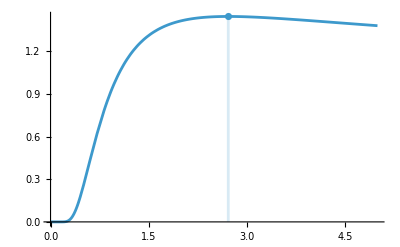

```mathematica
f[x_]:= x^(1/x)
Limit[f[x],x->0,Direction->"FromAbove"]
Limit[f[x],x->Infinity]
Maximize[f[x],x]
Show[Plot[f[x],{x,0, 5}],DiscretePlot[f[x],{x,{E}},ColorFunction->"Rainbow"]]
```

```mathematica
ClearAll[x,n]
SumConvergence[(n!)^2*x^n/(2n)!,n]
```

Abs[x]<4

{-2 ⅇ^(-t^2/2),-1.5 ⅇ^(-t^2/2),-ⅇ^(-t^2/2),-0.5 ⅇ^(-t^2/2),0,0.5 ⅇ^(-t^2/2),ⅇ^(-t^2/2),1.5 ⅇ^(-t^2/2),2 ⅇ^(-t^2/2)}

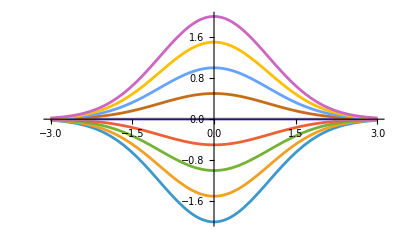

```mathematica
reseni = Table[DSolveValue[{y'[t]==-t*y[t],y[0]==y0},y[t],t],{y0, {-2,-1.5,-1,-0.5,0,0.5,1,1.5,2}}]
Plot[reseni, {t, -3, 3}]
```

```mathematica
egypt[0]={};
egypt[q_]:=Flatten[{1/Ceiling[1/q],egypt[q-1/Ceiling[1/q]]}]
```

```mathematica
egypt[505/5111]
```

{1/11,1/127,1/42755,1/16959642477,1/5177330513040968877045}

```mathematica
Total[]
```

505/5111

```mathematica
f[n_,x_,i_]/;i<=n:=Sqrt[1+(i+1)*f[n,x,i+1]]
f[n_,x_,i_]/;i>n:=Sqrt[1+x]
```

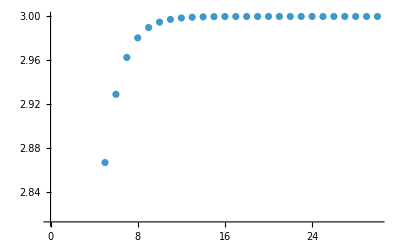

```mathematica
ListPlot[Table[{i,f[i,0,1]},{i,1,30}]]
```

```mathematica
"f(n,0)->3,n->Infinity"
```